```mathematica
z = x + ⅈ y
```

x+ⅈ y

## Linear Transformation (w = Az + B)

```mathematica
w[z_] := A z + B
```

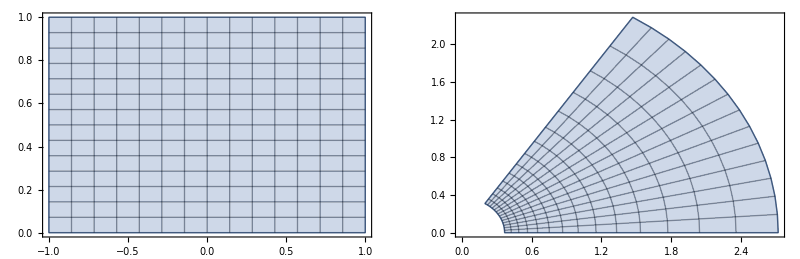

```mathematica
A = 4+ 4ⅈ;
B = 3 + 3ⅈ;
zPlane = ParametricPlot[{Re[z],Im[z]},{x,-1,1},{y,0,1}, Mesh->Full];
wPlane = ParametricPlot[{Re[w[z]],Im[w[z]]},{x,-1,1},{y,0,1}, Mesh->Full];
GraphicsGrid[{{zPlane, wPlane}}]
```

## Power Transformation (w = z^n)

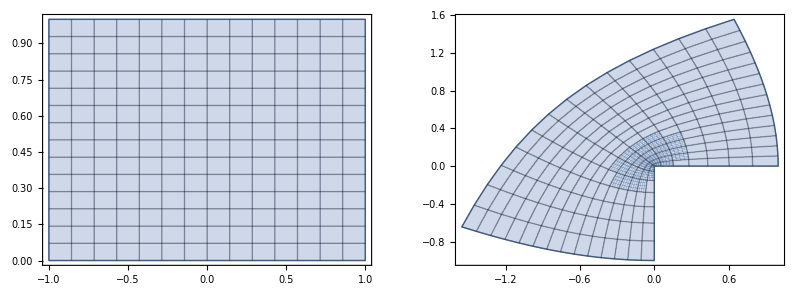

```mathematica
w[z_] := z^(3/2)
zPlane = ParametricPlot[{Re[z],Im[z]},{x,-1,1},{y,0,1}, Mesh->Full];
wPlane = ParametricPlot[{Re[w[z]],Im[w[z]]},{x,-1,1},{y,0,1}, Mesh->Full];
GraphicsGrid[{{zPlane, wPlane}}]
```

## Logarithmic and Exponential Transformation (w = Log[z] and w=Exp[z])

```mathematica
w[z_] := Exp[z]
zPlane = ParametricPlot[{Re[z],Im[z]},{x,-1,1},{y,0,1}, Mesh->Full];
wPlane = ParametricPlot[{Re[w[z]],Im[w[z]]},{x,-1,1},{y,0,1}, Mesh->Full];
GraphicsGrid[{{zPlane, wPlane}}]
```

-Graphics-

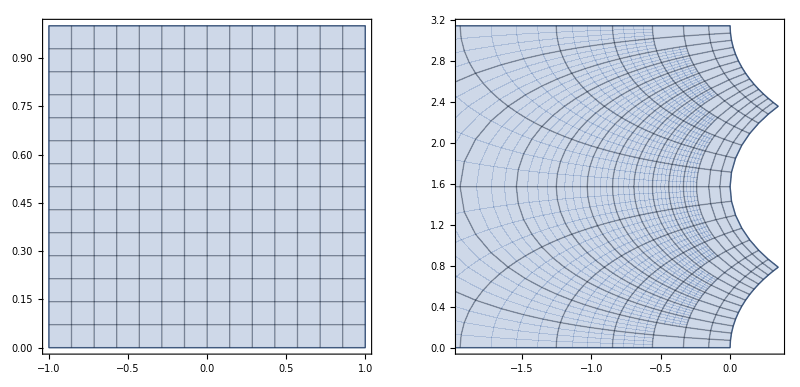

```mathematica
w[z_] := Log[z]
zPlane = ParametricPlot[{Re[z],Im[z]},{x,-1,1},{y,0,1}, Mesh->Full];
wPlane = ParametricPlot[{Re[w[z]],Im[w[z]]},{x,-1,1},{y,0,1}, Mesh->Full];
GraphicsGrid[{{zPlane, wPlane}}]
```

## Hyperbolic Transformation

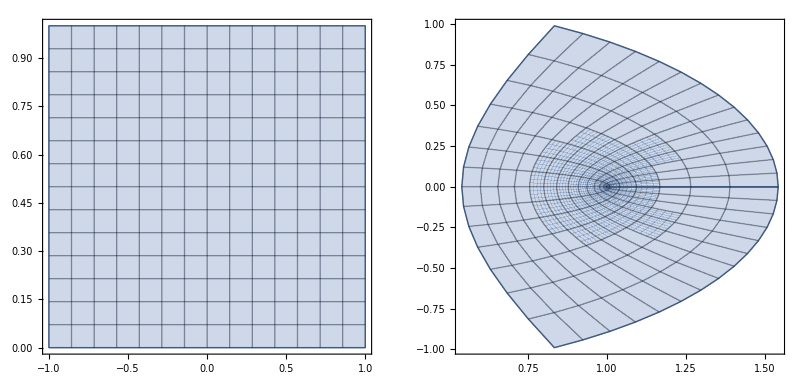

```mathematica
w[z_] := Cosh[z]
zPlane = ParametricPlot[{Re[z],Im[z]},{x,-1,1},{y,0,1}, Mesh->Full];
wPlane = ParametricPlot[{Re[w[z]],Im[w[z]]},{x,-1,1},{y,0,1}, Mesh->Full];
GraphicsGrid[{{zPlane, wPlane}}]
```